# From Chemical Mechanisms to Systems of Ordinary Differential Equations

Anton Antonov

Kristen Aramphanapon

book for Wiley 2009-2010

Discuss chemical kinetics. Describe the process of deriving of a system of ODE’s from a system of chemical equations. Discuss the symbols, and data structures needed for parsing of the chemical formulas into ODE’s. Give an exercise that asks to enhance the parsing to take temperature and altitude.

## Introduction

What are chemical reaction rates.

What are chemical kinetics mechanisms and why we need them.

Each equation describes a process of the transformation of a (well mixed) combination of compounds into another well mixed combination of compounds. In order to describe the speed of the process we need to introduce a function that describes the speed of conversion that depends upon time and concentrations.

System of Ordinary Differential Equations (SODE).

## Reaction kinetics

### Rate constants

### Unimolecular reactions

### Bimolecular reactions

### Temperature dependence of the rate constant

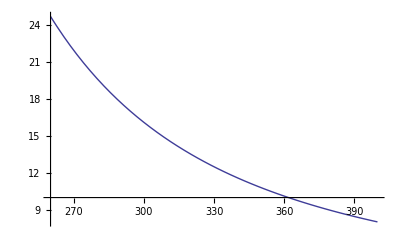

```mathematica
{A,R,Ea}={1,.12,100};
Plot[A Exp[Ea/(R T)],{T,260,400},PlotRange->All]
```

## Reaction paths / Chemical kinetic mechanisms

## Generating systems of ODE's

In order to understand the booking type of process used to generate the system ODE's corresponding to a chemical kinetic mechanism.

### Small example (manual)

Generate manually the corresponding system of ODE's for this mechanism:

```mathematica
testReactions={"N2O5"->"NO2"+"NO3","NO2"+"NO3"->"N2O5","NO2"+"NO3"->"NO"+"O2"+"NO2","NO"+"NO3"->2"NO2"};
testReactions//ColumnForm
```

N2O5→NO2+NO3
NO2+NO3→N2O5
NO2+NO3→NO+NO2+O2
NO+NO3→2 NO2

Assuming the third reaction is very slow compared to the rest, solve SODE for NO and NO3 as a system of algebraic equations.

The corresponding system of ODE's:

```mathematica
eqs//ColumnForm
```

c^(0,1)(NO3,t)==c(N2O5,t) k(1,t)-c(NO2,t) c(NO3,t) k(2,t)-c(NO2,t) c(NO3,t) k(3,t)-c(NO,t) c(NO3,t) k(4,t)
c^(0,1)(NO,t)==c(NO2,t) c(NO3,t) k(3,t)-c(NO,t) c(NO3,t) k(4,t)
c^(0,1)(O2,t)==c(NO2,t) c(NO3,t) k(3,t)

If r=∂ c(NO3,t)/∂ t then using Solve we get:

```mathematica
Solve[eqs/.{Derivative[0,1][c]["NO3",t]->0,Derivative[0,1][c]["NO",t]->0,Derivative[0,1][c]["O2",t]->r},{r,c["NO3",t],c["NO",t]}]//First//ColumnForm
```

r→(c(N2O5,t) k(1,t) k(3,t))/(k(2,t)+2 k(3,t))
c(NO,t)→(c(NO2,t) k(3,t))/(k(4,t))
c(NO3,t)→(c(N2O5,t) k(1,t))/(c(NO2,t) (k(2,t)+2 k(3,t)))

### Larger example (programming)

From the example above we can see that if we want to automatically generate the system of ODE's that corresponds to a chemical mechanism we have to program various bookkeeping functionalities. Since each ODE is produced for a given compound, we need to find all reactions which have that compound.

## Exercises

### Extend the SODE generator to use variables for temperature and altitude (or pressure)

Reference

[1] From Air Pollution to Climate Change

Other chemical kinetics groups